## Database Needs

```mathematica
Needs["DatabaseLink`"]
```

```mathematica
conn=OpenSQLConnection[JDBC["MySQL(Connector/J)","127.0.0.1:3306/sim_v3_10_18_2016"],"Username"->"root","Password"->""]
```

JDBC::error: Could not connect: Unknown database 'sim_v3_10_18_2016'

$Failed

## Data Extraction Functions

### General Data

```mathematica
Clear[Person];
Person=Association[{}];
```

```mathematica
getPerson[{id___Integer},{props__}]:=Module[{query,rawData,data,rule,propList,keys}, 
query="SELECT PersonID, Time, "<>(Sequence@@Riffle[{props},", "])<>" FROM PersonValues where PersonID="<>Sequence@@Riffle[ToString/@{id}," or PersonID="];
rawData=SQLExecute[conn,query];
If[MatchQ[rawData,{}],Return[]];
propList= {"Time",props};
rule=Map[#[[1,1]]->Association[Thread[Rule[propList,Rest@Transpose[#]]]]&,GatherBy[rawData,First]];
keys = Keys[Person];
MapThread[
If[MemberQ[keys,#1],
AppendTo[Person[#1],Values[#2]],
AppendTo[Person,#2]]&,
{{id},rule}];
];
```

```mathematica
getPerson[{id___Integer},{props__},Time_]:=Module[{query,rawData,data,rule,propList,keys}, 
query="SELECT PersonID, Time, "<>(Sequence@@Riffle[{props},", "])<>" FROM PersonValues where (PersonID="<>Sequence@@Riffle[ToString/@{id}," or PersonID="]<>") and Time < "<>ToString[Time];
rawData=SQLExecute[conn,query];
If[MatchQ[rawData,{}],Return[]];
propList= {"Time",props};
rule=Map[#[[1,1]]->Association[Thread[Rule[propList,Rest@Transpose[#]]]]&,GatherBy[rawData,First]];
keys = Keys[Person];
MapThread[
If[MemberQ[keys,#1],
AppendTo[Person[#1],Values[#2]],
AppendTo[Person,#2]]&,
{{id},rule}];
]
```

```mathematica
getPerson[{id___Integer},{props__},Time1_,Time2_]:=Module[{query,rawData,data,rule,propList,keys}, 
query="SELECT PersonID, Time, "<>(Sequence@@Riffle[{props},", "])<>" FROM PersonValues where (PersonID="<>Sequence@@Riffle[ToString/@{id}," or PersonID="]<>") and (Time > "<>ToString[Time1]<>" and Time < "<>ToString[Time2]<>")";
Print[query];
rawData=SQLExecute[conn,query];
If[MatchQ[rawData,{}],Return[]];
propList= {"Time",props};
rule=Map[#[[1,1]]->Association[Thread[Rule[propList,Rest@Transpose[#]]]]&,GatherBy[rawData,First]];
keys = Keys[Person];
MapThread[
If[MemberQ[keys,#1],
AppendTo[Person[#1],Values[#2]],
AppendTo[Person,#2]]&,
{{id},rule}];
]
```

### Population Data

```mathematica
computeProbability[data_]:=Module[{d,AllSizes,AllCounts,TotalProb,Probs},
d = SortBy[Tally[data],First];
AllSizes = d[[All,1]];
AllCounts=d[[All,2]];
TotalProb = Total[d/.{{s_Integer,n_Integer}:>s*n}];
Probs=Table[Total[d[[i;;-1]]/.{{s_Integer,n_Integer}:>s*n}]/TotalProb,{i,Length[AllCounts]}];
Thread[{Sort@AllSizes,Probs}]
];
```

```mathematica
ar=0.5;
```

```mathematica
getLogData[db_String]:=Module[{res,conn,data,d,pd,model,line,r2},
{SIRBlue=RGBColor[0.2,0.2,0.7],SIRRed=RGBColor[0.7,0.2,0.2],SIRGreen=RGBColor[0.2,0.7,0.2],SIRBlack=RGBColor[0.,0.,0.]};
res=Association[{}];
conn = OpenSQLConnection[JDBC["MySQL(Connector/J)","127.0.0.1:3306/"<>db],"Username"->"root","Password"->""];
data = SQLSelect[conn,"HistoryData",{"Time","Infected"}][[1000;;-1]];
d = Map[Total,DeleteCases[Split[data[[All,2]],#!=0&],{0}]];
pd=computeProbability[d];
model = LinearModelFit[Log@pd[[1;;Floor[0.8 Length[pd]]]],x,x];
line = model["BestFit"];
r2 = model["RSquared"];
{sr,fr}=model[{"StandardizedResiduals", "FitResiduals"}];

AppendTo[res,"Epidemic Data"->ListPlot[d,
PlotStyle->{{Thick,SIRRed}},
PlotRange->Full,
Frame->True,
FrameLabel->{Style["Epidemic Number",FontSize->26],Style["Epidemic Size",FontSize->26]},
LabelStyle->Directive[Medium, Bold],
ImageSize->Large,PlotStyle->96,Filling->Axis,AspectRatio->ar]];
AppendTo[res,"Histogram"->Histogram[d,20,ImageSize->Large,ChartElementFunction->"FadingRectangle",ChartStyle->Orange,Frame->True,FrameLabel->{Style["Epidemic Size",FontSize->26],Style["Count",FontSize->26]},AspectRatio->ar,LabelStyle->Directive[Medium, Bold]]];
AppendTo[res,"Log Probability Distribution"->ListLogLogPlot[pd,
Joined->True, 
Mesh->Full,
ImageSize->Large,
PlotRange->{Automatic,{Min[0.1,Min[pd]],1.1}},
Ticks->{Table[{10^k,Superscript[10,k]},{k,-2,5}],Table[{10^k,Superscript[10,k]},{k,-5,1,0.2}]},
GridLines->Automatic,
Frame->True,FrameLabel->{Style["Epidemic Size",FontSize->26],Style["Probability",FontSize->26]},AspectRatio->ar,LabelStyle->Directive[Medium, Bold]]];
AppendTo[res,"Log Distribution"->ListLogLogPlot[Reverse@Sort@d,
Joined->True, 
Mesh->Full,
ImageSize->Large,
GridLines->Automatic,
Frame->True,FrameLabel->{Style["Epidemic Size",Large],Style["Number of Occurence",Large]},AspectRatio->ar,LabelStyle->Directive[Medium, Bold]]];
AppendTo[res,"Statistics Model"->model];
AppendTo[res,"Linear Model"->Plot[line,{x,0,pd[[-1,1]]},PlotRange->Full,PlotStyle->{Thick,Orange},AspectRatio->ar]];
AppendTo[res,"R^2 Value"->r2];
AppendTo[res,"Error Statistics"->{sr,fr}];
AppendTo[res,"Model Parameters"->model["ParameterTable"]];
res
]
```

### Individual Data

```mathematica
extractPerson[id_,{props__}]:=Module[{},
Map[Thread[{Person[id]["Time"],Person[id][#]}]&,
{props}]
]
```

### Contact Network Functions

```mathematica
getConnections[]:=Module[{conquery,perquery,conData,personIDs,perData},
conquery="SELECT PersonA, PersonB, Weight FROM Connections";
conData=SQLExecute[conn,conquery]
]
```

### Graph

```mathematica
conn
```

$Failed

```mathematica
getGraph[{id___}]:=Module[{conquery,perquery,conData,personIDs,perData},
conquery="SELECT PersonA, PersonB, Weight FROM Connections where (PersonA="<>Sequence@@Riffle[ToString/@{id}," or PersonA="]<>")"<>" or (PersonB="<>Sequence@@Riffle[ToString/@{id}," or PersonB="]<>")";
conData=SQLExecute[conn,conquery];
connections = conData[[All,1;;2]]/.{{a_,b_}:>a<->b};
weights = conData[[All,3]];
Graph[connections]
]
```

## Plotting Functions

```mathematica
{SIRBlue=RGBColor[0.2,0.2,0.7],SIRRed=RGBColor[0.7,0.2,0.2],SIRGreen=RGBColor[0.2,0.7,0.2],SIRBlack=RGBColor[0.,0.,0.]}
```

{RGBColor[0.2, 0.2, 0.7],RGBColor[0.7, 0.2, 0.2],RGBColor[0.2, 0.7, 0.2],RGBColor[0., 0., 0.]}

```mathematica
PopulationDataPlot[data_,opts___]:=ListLinePlot[data,
PlotStyle->{{Thick,SIRBlue},{Thick, SIRRed},{Thick, SIRGreen},{Thick, SIRBlack}},
(*PlotLegends->Placed[{"Susceptible","Infected","Recovered","Dead"},Above],*)
Frame->True,
FrameLabel->{Style["Time",Large],Style["Population",Large]},
LabelStyle->Directive[Medium, Bold],
ImageSize->Large,
opts]
```

```mathematica
CellDataPlot[data_,opts___]:=ListLinePlot[data,
PlotStyle->{{Thick, SIRBlue,Dashed},{Thick, SIRRed,Dotted},{Thick, SIRGreen},{Thick, SIRBlack}},
PlotLegends->Placed[{"Susceptible Cells","Infected Cells","Viral Load"},Right],
Frame->True,
FrameLabel->{Style["Time (days)",Medium],Style["Cells",Medium]},
LabelStyle->Directive[Medium, Bold],
ImageSize->Large,
opts]
```

## Contact Network

### Connecting to Database

```mathematica
conn=OpenSQLConnection[JDBC["MySQL(Connector/J)","127.0.0.1:3306/sim_v1_11_14_2016"],"Username"->"root","Password"->""]
```

SQLConnection[…]

```mathematica
allData=getConnections[];
```

```mathematica
data=DeleteDuplicates[Map[{#[[1,1,1]],#[[1,1,2]],Total[#[[All,-1]]]}&,GatherBy[Join[allData/.{{a_,b_,c_}:>{{a,b},c}},allData/.{{a_,b_,c_}:>{{b,a},c}}],First]]];
```

```mathematica
dd=Join[allData/.{{a_,b_,c_}:>{a,b,c}},allData/.{{a_,b_,c_}:>{b,a,c}}];
```

```mathematica
finalData=Join[Complement[Tuples[Range[120],2],data[[All,1;;2]]]/.{{a_,b_}:>{a,b,0}},data];
```

```mathematica
m = Max[finalData[[All,-1]]];
```

```mathematica
diag=False;
```

```mathematica
finalData = If[diag,finalData /. {{a_, b_, c_} :> If[a == b, {a, b, Max[Cases[finalData,{a,_,_}][[All,3]]]}, {a, b, c}]},finalData];
```

```mathematica
scaledData = finalData/.{{a_,b_,c_}:>{a,b,c/m}};
```

```mathematica
conNet=ListDensityPlot[dd,PlotLegends->False,ImageSize->Large,PlotRange->{{0,80},{0,80},All},ColorFunction->(RGBColor[#,#,#]&),ColorFunctionScaling->True,PlotTheme->"Business",InterpolationOrder->1,FrameLabel->{Style["Age",22],Style["Age",22]}]
```

-Graphics-

Export["/Users/sahand/Research/paper1/SOC-SIR/images/contactnetwork.jpg", conNet, "jpeg"];

## History Data

### Connect to Database

```mathematica
CloseSQLConnection/@SQLConnections[];
db="sim_v13_1_6_2017";
```

```mathematica
conn=OpenSQLConnection[JDBC["MySQL(Connector/J)","127.0.0.1:3306/"<>db],"Username"->"root","Password"->""]
```

SQLConnection[…]

### Extract data

```mathematica
{SIRBlue=RGBColor[0.2,0.2,0.7],SIRRed=RGBColor[0.7,0.2,0.2],SIRGreen=RGBColor[0.2,0.7,0.2],SIRBlack=RGBColor[0.,0.,0.]}
```

{RGBColor[0.2, 0.2, 0.7],RGBColor[0.7, 0.2, 0.2],RGBColor[0.2, 0.7, 0.2],RGBColor[0., 0., 0.]}

```mathematica
HistoryData=SQLSelect[conn,"HistoryData"];
```

```mathematica
res:=getLogData[db]
```

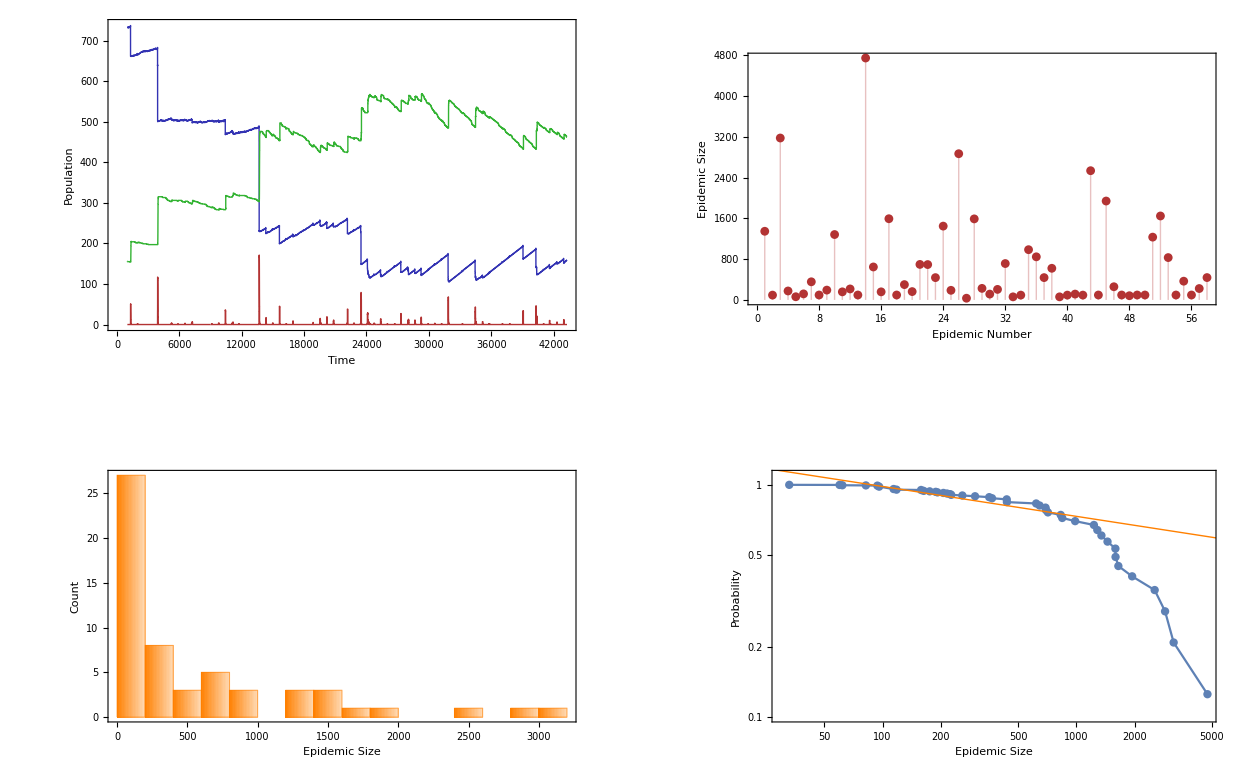

```mathematica
p=PopulationDataPlot[Table[Thread[{HistoryData[[1000;;-1,2]],HistoryData[[1000;;-1,i]]}],{i,{3,5,6}}]];
i=res["Epidemic Data"];
h=res["Histogram"];
l=Show[{res["Log Probability Distribution"],res["Linear Model"]}];
GraphicsGrid[{{p,i},{h,l}}]
```

## Error Trend

```mathematica
xticks = {"Stage 1", "Stage 2", "Stage 3", "Stage 4","Stage 5","Stage 6","Stage 7"};
```

```mathematica
dbs = {"sim_v1_11_14_2016","sim_v1_10_31_2016","sim_v2_11_15_2016","sim_v3_11_15_2016","sim_v1_10_24_2016","sim_v1_10_23_2016","sim_v3_10_30_2016"}
```

{sim_v1_11_14_2016,sim_v1_10_31_2016,sim_v2_11_15_2016,sim_v3_11_15_2016,sim_v1_10_24_2016,sim_v1_10_23_2016,sim_v3_10_30_2016}

```mathematica
ress=getLogData/@dbs;
```

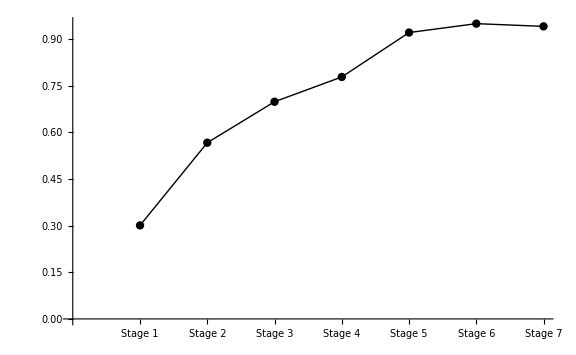

```mathematica
ListLinePlot[ress[[#]]["R^2 Value"]&/@Range[Length[dbs]],Ticks->{Thread[{Range[Length[dbs]],Rotate[#,Pi/3]&/@xticks}],Automatic},ImageSize->Large,Mesh->Full,PlotStyle->{Black,Thick}]
```

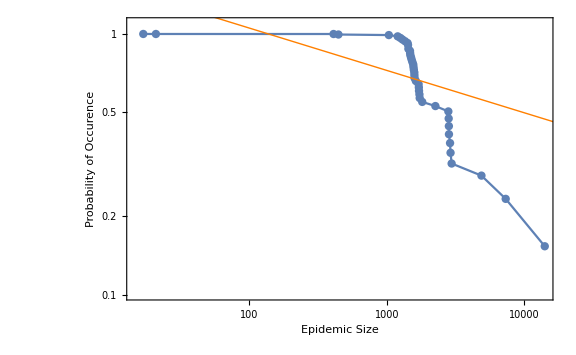

```mathematica
res:=getLogData["sim_v1_11_14_2016"];
Show[{res["Log Probability Distribution"],res["Linear Model"]}]
```

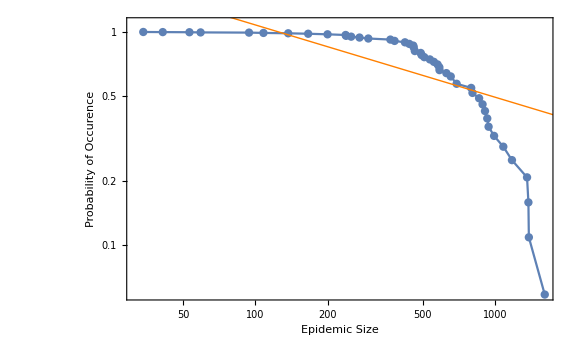

```mathematica
res:=getLogData["sim_v1_10_31_2016"];
Show[{res["Log Probability Distribution"],res["Linear Model"]}]
```

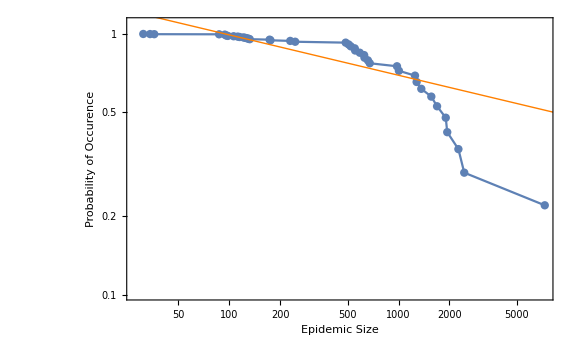

```mathematica
res:=getLogData["sim_v2_11_15_2016"];
Show[{res["Log Probability Distribution"],res["Linear Model"]}]
```

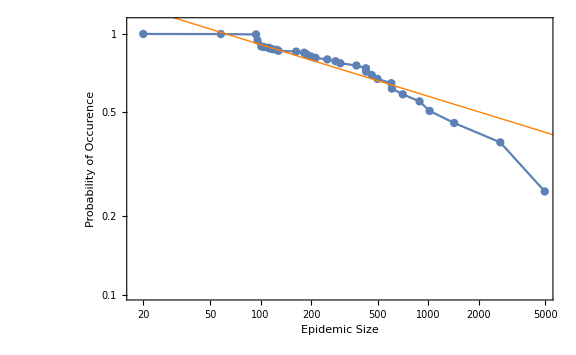

```mathematica
res:=getLogData["sim_v3_10_24_2016"];
Show[{res["Log Probability Distribution"],res["Linear Model"]}]
```

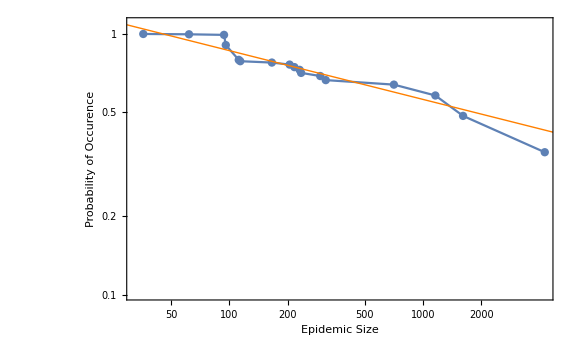

```mathematica
res:=getLogData["sim_v1_10_24_2016"];
Show[{res["Log Probability Distribution"],res["Linear Model"]}]
```

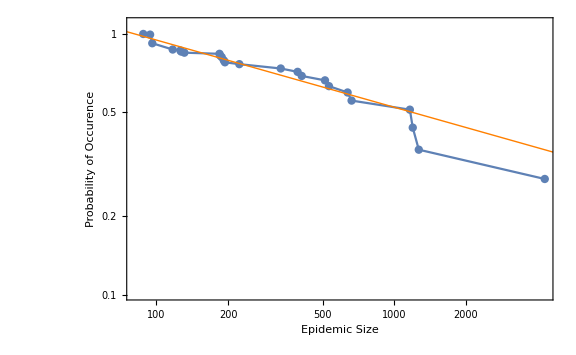

```mathematica
res:=getLogData["sim_v1_10_23_2016"];
Show[{res["Log Probability Distribution"],res["Linear Model"]}]
```

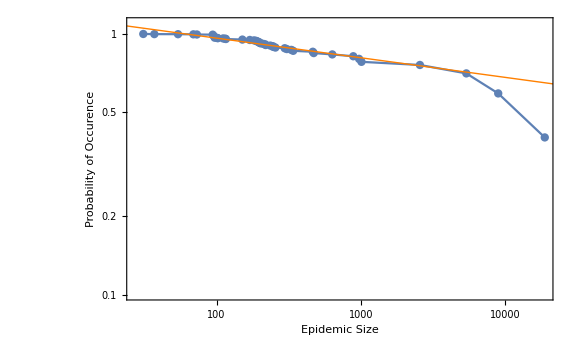

```mathematica
res:=getLogData["sim_v3_10_30_2016"];
Show[{res["Log Probability Distribution"],res["Linear Model"]}]
```

## Multiple Error Trend

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
xticks =Map[Style[#,FontSize->18]&, {"Stage 1", "Stage 2", "Stage 3", "Stage 4","Stage 5","Stage 6"}];
```

```mathematica
dbs0 = {"sim_v1_11_14_2016","sim_v1_10_31_2016","sim_v2_11_15_2016","sim_v3_11_15_2016","sim_v1_10_24_2016","sim_v1_10_23_2016"};
dbs1 = {"sim_v1_11_26_2016","sim_v7_11_27_2016","sim_v4_11_27_2016","sim_v10_11_28_2016","sim_v13_11_28_2016","sim_v16_11_28_2016"};
dbs2 = {"sim_v2_11_26_2016","sim_v8_11_28_2016","sim_v5_11_27_2016","sim_v11_11_28_2016","sim_v14_11_28_2016","sim_v17_11_28_2016"};
dbs3 = {"sim_v3_11_26_2016","sim_v9_11_28_2016","sim_v6_11_27_2016","sim_v12_11_28_2016","sim_v15_11_28_2016","sim_v18_11_29_2016"};
```

```mathematica
ress0=getLogData/@dbs0;
err0 =ress0[[#]]["R^2 Value"]&/@Range[Length[dbs0]];
```

```mathematica
ress1=getLogData/@dbs1;
err1 =ress1[[#]]["R^2 Value"]&/@Range[Length[dbs1]];
```

```mathematica
ress3=getLogData/@dbs3;
err3 =ress3[[#]]["R^2 Value"]&/@Range[Length[dbs3]];
```

```mathematica
ress2=getLogData/@dbs2;
err2 =ress2[[#]]["R^2 Value"]&/@Range[Length[dbs2]];
```

```mathematica
data = MapThread[{Mean[{#1,#2,#3,#4}],StandardDeviation[{#1,#2,#3,#4}]/2}&,{err0,err1,err2,err3}]
```

{{0.329563,0.0234402},{0.680672,0.0363657},{0.727903,0.0531907},{0.769333,0.0449336},{0.867828,0.00986224},{0.925249,0.0160809}}

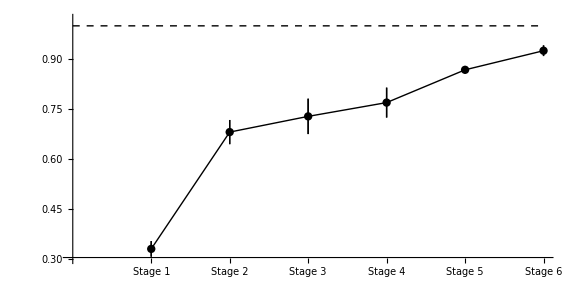

```mathematica
errImage=Show[{
ErrorListPlot[data,Joined->True,PlotRange->{Automatic,{0.3,1.02}},Ticks->{Thread[{Range[Length[dbs1]],Rotate[#,Pi/3]&/@xticks}],Automatic},ImageSize->Large,Mesh->Full,PlotStyle->{Black,Thick},AxesLabel->{Style["Increasing Complexity",Large],Style["Correlation Coefficient",Large]}],
Plot[1,{x,0,6},PlotStyle->{Black,Thick,Dashed}]
},AspectRatio->0.5]
```

```mathematica
errImage=-Graphics-
```

-Graphics-

```mathematica
errImage=Labeled[errImage,Rotate[Style["Correlation Coefficient",FontColor->Gray,FontSize->Large,FontWeight->Bold,FontFamily->"Helvetica"],Pi/2],Left]
```

-Graphics-Correlation Coefficient

Export["/Users/sahand/Research/paper1/SOC-SIR/images/Variation_Sweep.jpg", errImage]

"/Users/sahand/Research/paper1/SOC-SIR/images/Variation_Sweep.jpg"

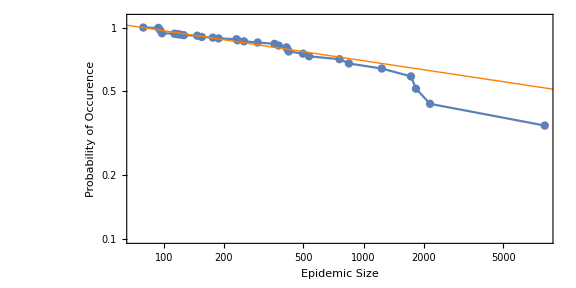

```mathematica
powerlaw=Show[ress3[[6]][#]&/@{"Log Probability Distribution","Linear Model"}]
```

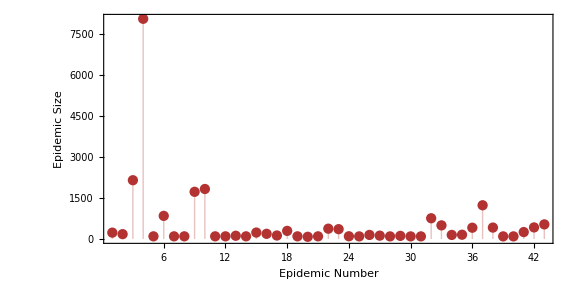

```mathematica
epidemic=Show[ress3[[6]][#]&/@{"Epidemic Data"}]
```

Export["/Users/sahand/Research/paper1/SOC-SIR/images/PowerLaw.jpg", powerlaw]

"/Users/sahand/Research/paper1/SOC-SIR/images/PowerLaw.jpg"

Export["/Users/sahand/Research/paper1/SOC-SIR/images/EpidemicTimeHistory.jpg", epidemic]

"/Users/sahand/Research/paper1/SOC-SIR/images/EpidemicTimeHistory.jpg"

```mathematica
Manipulate[Labeled[Show[ToExpression[res][[n]][#]&/@{"Log Probability Distribution","Linear Model"}],ToExpression[res][[n]]["R^2 Value"],Top],{n,1,6,1},{res,{"ress0","ress1","ress2","ress3"}}]
```

## Stages

```mathematica
dbs0 = {"sim_v1_11_14_2016","sim_v1_10_31_2016","sim_v2_11_15_2016","sim_v3_11_15_2016","sim_v1_10_24_2016","sim_v1_10_23_2016"};
dbs1 = {"sim_v1_11_26_2016","sim_v7_11_27_2016","sim_v4_11_27_2016","sim_v10_11_28_2016","sim_v13_11_28_2016","sim_v16_11_28_2016"};
dbs2 = {"sim_v2_11_26_2016","sim_v8_11_28_2016","sim_v5_11_27_2016","sim_v11_11_28_2016","sim_v14_11_28_2016","sim_v17_11_28_2016"};
dbs3 = {"sim_v3_11_26_2016","sim_v9_11_28_2016","sim_v6_11_27_2016","sim_v12_11_28_2016","sim_v15_11_28_2016","sim_v18_11_29_2016"};
```

```mathematica
ress0=getLogData/@dbs0;
err0 =ress0[[#]]["R^2 Value"]&/@Range[Length[dbs0]];
```

```mathematica
ress1=getLogData/@dbs1;
err1 =ress1[[#]]["R^2 Value"]&/@Range[Length[dbs1]];
```

```mathematica
ress2=getLogData/@dbs2;
err2 =ress2[[#]]["R^2 Value"]&/@Range[Length[dbs2]];
```

```mathematica
ress3=getLogData/@dbs3;
err3 =ress3[[#]]["R^2 Value"]&/@Range[Length[dbs3]];
```

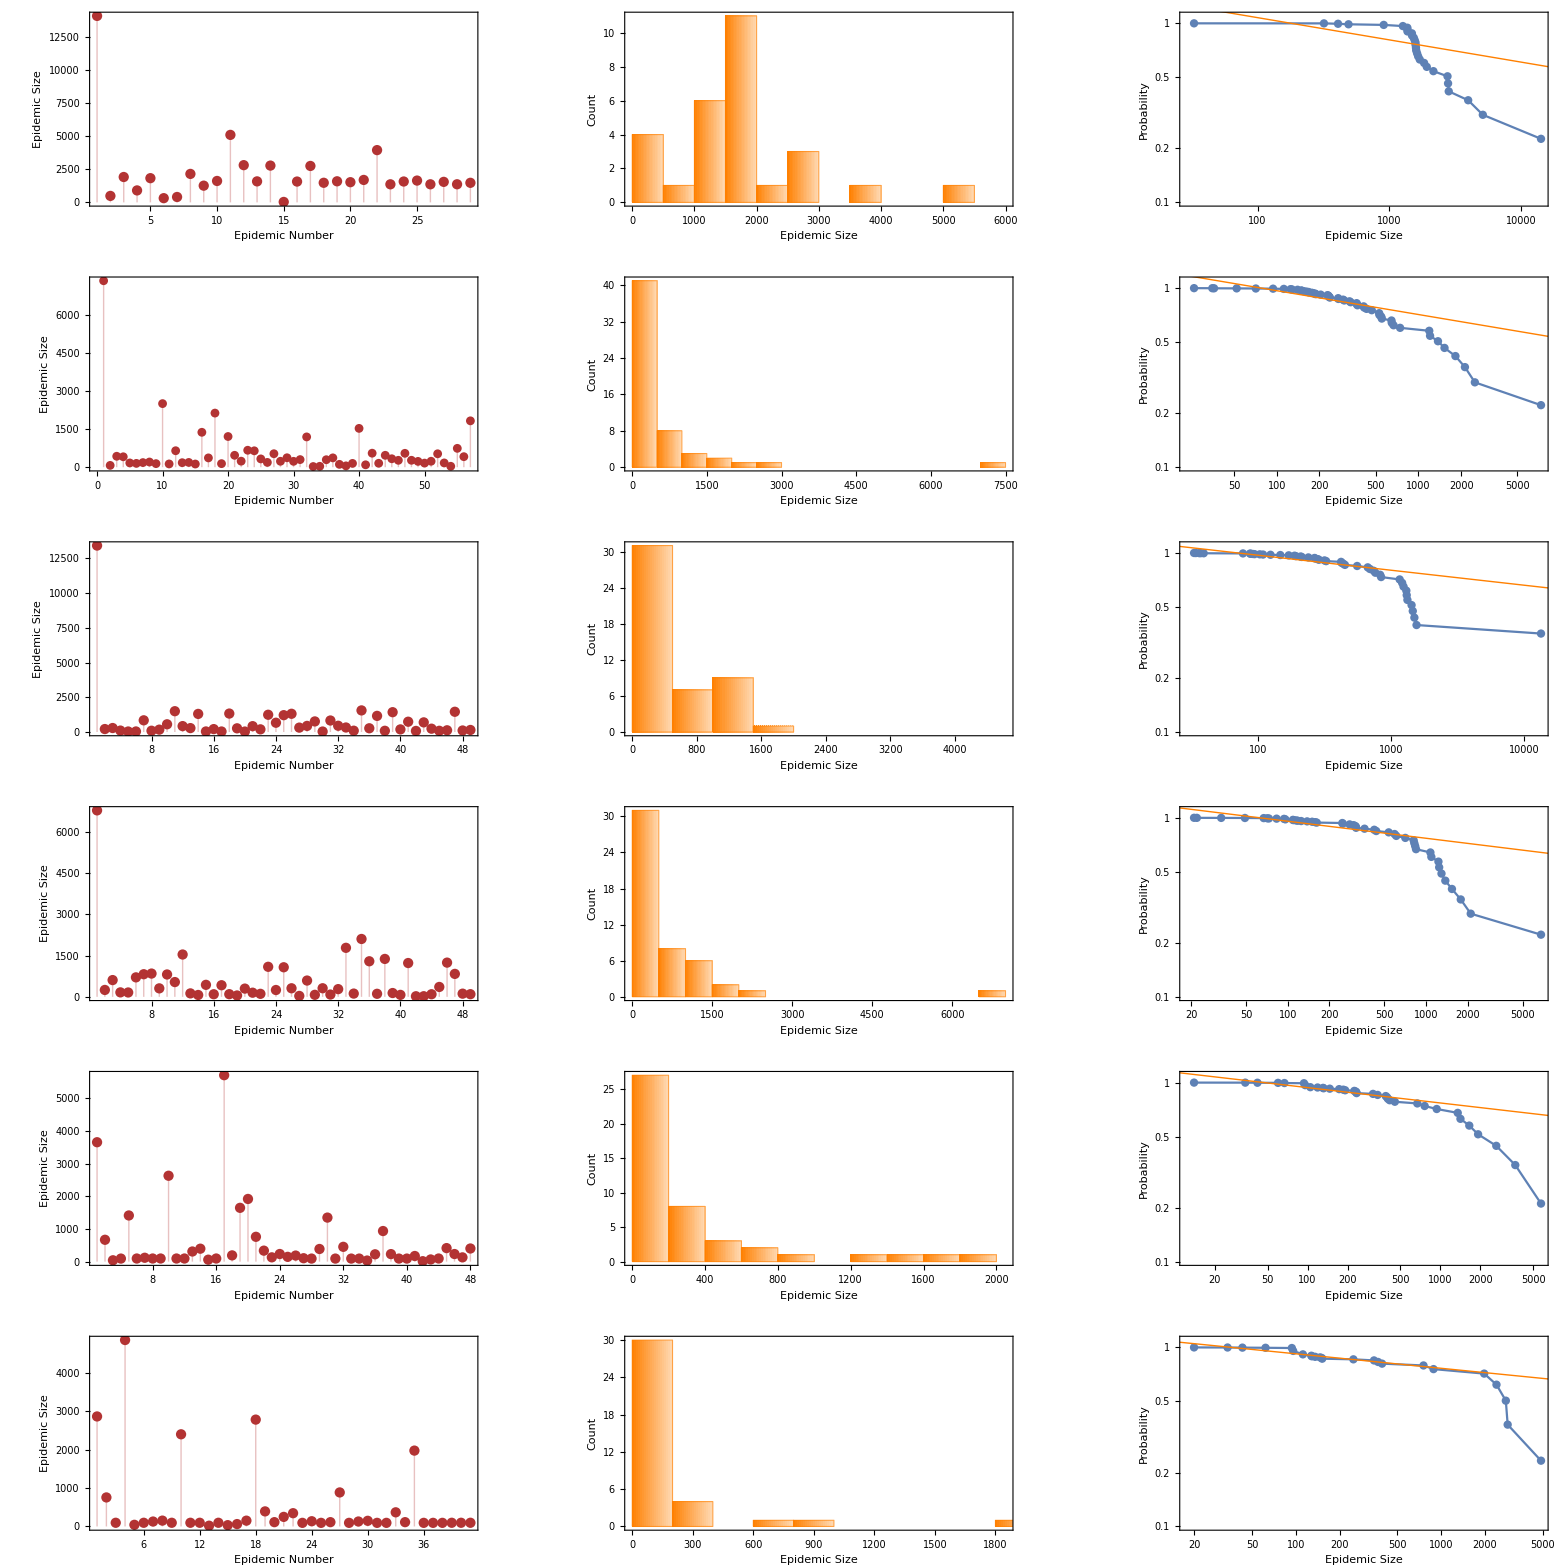

```mathematica
GraphicsGrid[
Map[
{#["Epidemic Data"],#["Histogram"],Show[{#["Log Probability Distribution"],#["Linear Model"]}]}
&,ress2]
]
```

```mathematica
plots=Map[
GraphicsRow@{#["Epidemic Data"],#["Histogram"],Show[{#["Log Probability Distribution"],#["Linear Model"]}]}
&,ress2];
```

MapIndexed[Export["/Users/sahand/Research/paper1/SOC-SIR/images/stage_" <> ToString[#2[[1]]] <> ".jpg", #1] &, plots]

{"/Users/sahand/Research/paper1/SOC-SIR/images/stage_1.jpg", "/Users/sahand/Research/paper1/SOC-SIR/images/stage_2.jpg", "/Users/sahand/Research/paper1/SOC-SIR/images/stage_3.jpg", "/Users/sahand/Research/paper1/SOC-SIR/images/stage_4.jpg", "/Users/sahand/Research/paper1/SOC-SIR/images/stage_5.jpg", "/Users/sahand/Research/paper1/SOC-SIR/images/stage_6.jpg"}

## Individual Data

```mathematica
db="sim_v1_11_14_2016";
```

```mathematica
conn=OpenSQLConnection[JDBC["MySQL(Connector/J)","127.0.0.1:3306/"<>db],"Username"->"root","Password"->""]
```

SQLConnection[…]

```mathematica
pid = 3;
```

```mathematica
pid=78;
```

```mathematica
getPerson[{pid},{"SusCells","InfCells","VirLoads"},3050,3150];
```

SELECT PersonID, Time, SusCells, InfCells, VirLoads FROM PersonValues where (PersonID=78) and (Time > 3050 and Time < 3150)

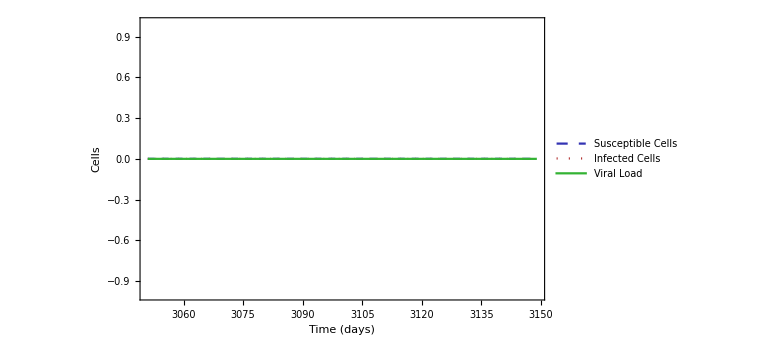

```mathematica
ihd=CellDataPlot[extractPerson[pid,{"SusCells","InfCells","VirLoads"}]]
```

Export["/Users/sahand/Research/paper1/SOC-SIR/images/IHD.jpg", ihd, "jpeg"];

## Network

```mathematica
conn=OpenSQLConnection[JDBC["MySQL(Connector/J)","127.0.0.1:3306/sim_v1_10_31_2016"],"Username"->"root","Password"->""]
```

SQLConnection[…]

```mathematica
getGraph[{1,2,3}]
```

$Aborted[]

```mathematica
N@GlobalClusteringCoefficient[getGraph[Range[1000]]]
```

0.986953

```mathematica
N@GlobalClusteringCoefficient[getGraph[Range[1000]]]
```

0.986953

```mathematica
N@MeanClusteringCoefficient[getGraph[Range[1000]]]
```

0.991386

```mathematica
N@MeanClusteringCoefficient[getGraph[Range[1000]]]
```

0.987345

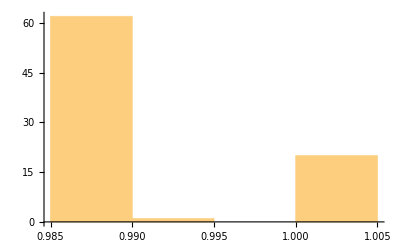

```mathematica
Histogram[N@LocalClusteringCoefficient[getGraph[Range[1000]]]]
```

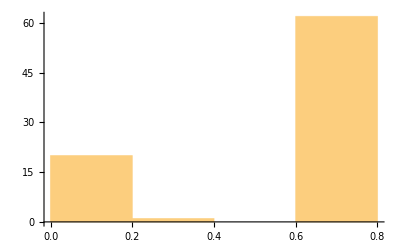

```mathematica
Histogram[BetweennessCentrality[getGraph[Range[1000]]]]
```

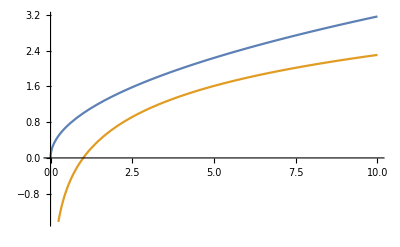

```mathematica
Plot[{Sqrt[x], Log[x]},{x,0,10}]
```